```mathematica
ClearAll["Global`*"]
```

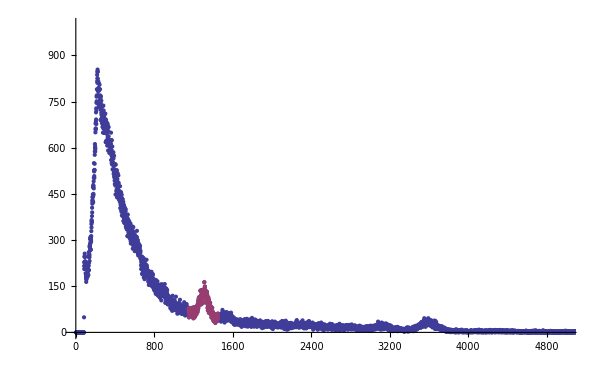

```mathematica
imp=Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\na.TKA","Table"];
data=Transpose[imp][[1]];
data=Table[{i,data[[i]]},{i,1,Length[data]}];
data2=Take[data,{1150,1450}];
ListPlot[{data,data2},PlotRange->{{0,5000},{0,1000}},ImageSize->600]
```

FittedModel[147.642+74.8791 ⅇ^(-0.000289841 («1»)^2)-0.070816 x]

| Estimate | Standard Error | t-Statistic | P-Value
A | 74.8791 | 1.57002 | 47.693 | 5.72548×10^-141
x0 | 1306.16 | 0.99616 | 1311.2 | 3.76873231176009×10^-559
σ | -41.5342 | 1.21102 | -34.2969 | 4.00878×10^-105
u1 | 147.642 | 9.40037 | 15.706 | 7.48945×10^-41
u2 | -0.070816 | 0.00727342 | -9.73627 | 1.2936×10^-19

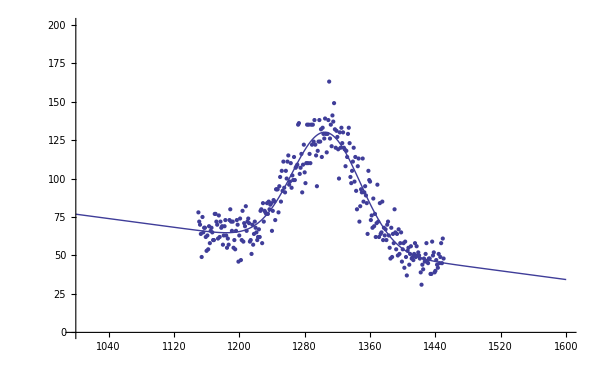

```mathematica
nlm=NonlinearModelFit[data2,A Exp[-1/2((x-x0)/σ)^2]+u1+u2 x,{A,{x0,1300},σ,u1,u2},x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,1000,1600},PlotRange->{0,200},ImageSize->600],ListPlot[data2]]
```